The Movie Database |

Wolfram Language interface to the Movie Database API

getCertifications | get certifications for movies and television
getChanges | database changes in the last 24 hours
getCollection | get collection of movies, e.g. trilogy
getCompany | get information on production companies
getConfiguration | get configuration information
getCredits | get credits (xxx)
getDiscover | discover movies of television shows using query syntax
getFind | find by external identifier, e.g. IMDB
getGenres | list genres
getKeyword | get keywords (xxx)
getLists | get user defined lists, e.g. favorites
getMovie | get movie details
getNetwork | get television network information
getPerson | get person details, e.g. actors
getProviders | get movie or television providers, e.g. Netflix
getReview | get review (xxx)
getSearch | search for movies, television, or persons
getTelevision | get television show details
getTelevisionSeason | get television show season details
getTelevisionEpisode | get television show episode details
getTelevisionEpisodeGroup | get television show group details
getTrending | get trending movies or television shows by identifier

Available functions.

#### Get certifications for movies and television

Certifications inform viewers about the intended audience and age group for a movie of television show.

Get certifications for movies, for all countries:

```mathematica
ds=getCertifications["movie"]
```

Focus on certifications for the United States, sorted in ascending order of restrictions:

```mathematica
ds["certifications","US"][SortBy[#order&]]
```

Get certifications for television shows:

```mathematica
getCertifications["tv"]
```

#### Database changes in the last 24 hours

Get the identifiers of movies whose entries have been changed in the last 24 hours:

```mathematica
getChanges["movie"]
```

-Graphics-

Same for television:

```mathematica
getChanges["tv"]
```

#### Get collections of movies

Get the collection for the "Lord of the Rings" movies:

```mathematica
getCollection[119]
```

Get the images related to this collection:

```mathematica
getCollection[119,"images"]
```

#### Get information on production companies

Get information on the "New Line Cinema" movie company:

```mathematica
getCompany[12]
```

```mathematica
getCompany[12,"images"]
```

#### Get configuration information

Get general configuration information, e.g. image base URLs:

```mathematica
getConfiguration[]
```

Get configuration information on countries:

```mathematica
getConfiguration["countries"]
```

#### Get credits (xxx)

```mathematica
getCredits[16]
```

#### Discover movies of television shows using query syntax

Details are documented here: https://developers.themoviedb.org/3/discover/movie-discover

Get movies from 2021 with Denzel Washington (id: 5292):

```mathematica
getDiscover["movie",{
"primary_release_year"->"2021",
"with_cast"->"5292"
}]
```

#### Find by external identifier

Look up a movie by IMDB identifier:

```mathematica
getFind["tt0068646","imdb_id"]
```

#### List genres

Get movie genres:

```mathematica
getGenres["movie"]
```

#### Get keywords (xxx)

```mathematica
getKeyword[42]
```

#### Get user lists

Get a movie list created by Travis Bell about the Marvel Universe:

```mathematica
getLists[1]
```

#### Get movie details

Movies currently in theaters:

```mathematica
getMovie["now_playing"]
```

Get details on the movie "The Fellowship of the Ring":

```mathematica
getMovie[120]
```

Get the credits:

```mathematica
getMovie[120,"credits"]
```

#### Get television network information

Get information about a television network, e.g. TNT:

```mathematica
getNetwork[41]
```

#### Get person details

Get popular persons:

```mathematica
getPerson["popular"]
```

Get details on actor Tom Holland:

```mathematica
getPerson[1136406]
```

#### Get review (xxx)

```mathematica
getReview[123]
```

#### Get movie or television providers

Get information on movie providers:

```mathematica
getProviders["movie"]
```

#### Search for movies, television, or persons

Search for "Lord of the Rings" movies:

```mathematica
getSearch["movie","Lord of the Rings"]
```

Search for movies with Denzel Washington:

```mathematica
getSearch["person","Denzel Washington"]
```

Search for the television show "Schitt's Creek":

```mathematica
getSearch["tv","Schitt's Creek"]
```

Search for the company "Paramount":

```mathematica
getSearch["company","Paramount"]
```

#### Get television show details

List television shows that are currently on the air:

```mathematica
getTelevision["on_the_air"]
```

Get details on the television show "Schitt's Creek":

```mathematica
getTelevision[61662]
```

#### Get television show season details

Get season details:

```mathematica
getTelevisionSeason[61662,6]
```

#### Get television show episode details

Get details on the series finale of "Schitt's Creek":

```mathematica
getTelevisionEpisode[61662,6,14]
```

#### Get television show group details

```mathematica
getTelevisionEpisodeGroup[1]
```

#### Get trending movies or television shows by identifier

Get movies that are currently trending:

```mathematica
getTrending["movie","day"]
```

Examples

The next sections shows how you can combine different function to retrieve specific content and generate specific reports.

#### Raiders of the Lost Ark

Search for movies matching with "raiders of the lost ark":

```mathematica
movies=getSearch["movie","raiders of the lost ark"];
movies["results"]
```

List the titles:

```mathematica
movies["results",All,"original_title"]
```

Get the identifier for the first movie listed:

```mathematica
id=movies["results",1,"id"]
```

85

Get details on the movie:

```mathematica
details=getMovie[id]
```

Print the overview of the movie:

```mathematica
Style[details["overview"],"Text"]
```

When Dr. Indiana Jones – the tweed-suited professor who just happens to be a celebrated archaeologist – is hired by the government to locate the legendary Ark of the Covenant, he finds himself up against the entire Nazi regime.

Get the configuration information, which includes base URLs for images:

```mathematica
config=getConfiguration[]
```

Build a poster image URL from the required elements, and import it:

```mathematica
url=URLBuild[{
config["images","secure_base_url"],
config["images","poster_sizes",2],
details["poster_path"]
}];
poster=Import[url]
```

-Graphics-

Similarly, build the URL for the backdrop image for the same movie:

```mathematica
url=URLBuild[{
config["images","secure_base_url"],
config["images","backdrop_sizes",2],
details["backdrop_path"]}];
backdrop=Import[url]
```

-Graphics-

#### Popular Movies in 2021

discover query syntax: https://developers.themoviedb.org/3/discover/movie-discover

Build a dataset for the 100 most popular movies of 2021:

```mathematica
datasets=Table[
Pause[.1];
getDiscover["movie",{
"primary_release_year"->"2021",
"sort_by"->"popularity.desc",
"page"->page
}]["results"],{page,5}];
```

```mathematica
ds=Join@@datasets
```

Get the movie identifiers for these movies:

```mathematica
ids=Normal[ds[All,"id"]]
```

{634649,524434,568124,425909,438695,811592,512195,624860,460458,860623,580489,644495,566525,739413,763788,843241,585245,589761,829358,516329,460465,459151,811072,787310,826749,438631,550988,754934,617653,370172,522402,756403,744275,508943,728526,436969,385128,877183,633802,482321,675445,523936,774741,592508,497698,763148,476669,685274,656991,451048,609972,337404,763164,772436,791373,818192,831223,770254,399566,823610,885110,672582,588228,581726,893941,762433,597208,876716,379686,568620,637649,646380,775943,525660,895001,639721,839436,887767,726684,423108,859041,623135,610253,820511,618162,527774,896221,632357,670429,768744,573164,754067,785538,630004,793967,796499,831827,614917,922017,895006}

Get movie details for each movie:

```mathematica
movies=Table[
Pause[.1];
getMovie[id]
,{id,ids}];
```

Join all the movie datasets together:

```mathematica
ds=Dataset[Join[Map[Normal,movies]]]
```

Plot the runtimes of the movies:

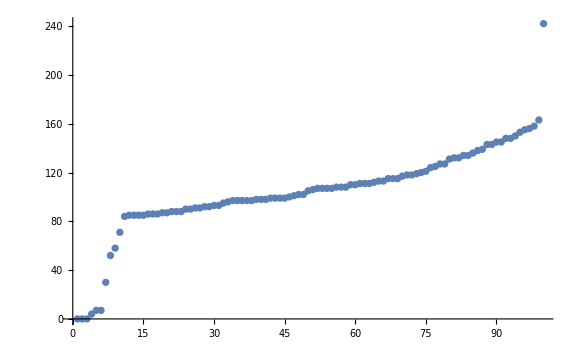

```mathematica
ds[All,"runtime"]//Normal//Sort//ListPlot[#,ImageSize->Large]&
```

Get the poster images for these popular movies:

```mathematica
config=getConfiguration[];
paths=Normal[ds[All,"poster_path"]];
posters=Map[
Function[{path},
Module[{url},
url=URLBuild[{
config["images","secure_base_url"],
config["images","poster_sizes",1],
path
}];
Import[url]
]],
paths];
```

Display the images in a grid:

```mathematica
ImageAssemble[Partition[ConformImages[posters],10]]
```

-Graphics-